# Trigonometria applicata alle distanze -Graphics-

-Graphics-

Prima di iniziare

```mathematica
Button["Carica Package", SetDirectory[NotebookDirectory[]]; << package.m, BaseStyle->{Red,40}]
```

Carica Package

Ci siamo quasi : manca solo un ultimo passaggio

1.	Vai sul menu “Evaluation”                                      -Graphics-


2.      E clicca su “Evaluate Notebook”						-Graphics-

# Da cosa vuoi iniziare ? -Graphics- -Graphics- -Graphics-

# TEORIA -Graphics-

-Graphics- | Durante le vacanze, Lorenzo va a Parigi. Di  fronte alla maestosità della 
tour Eiffel si chiede :"Ma quanto sarà alta?". Capendo di non poter srotolare 
un metro da sarta lungo più di  cento metri,si domanda se esista un modo 
più semplice di trovare una soluzione.  Noi siamo qui per mostrarvelo.

-Graphics-

## Cos’è la trigonometria?

La trigonometria è quella parte della matematica che studia i triangoli e le funzioni circolari. 
La sua utilità è quella di fornire informazioni sui triangoli a partire dai loro angoli e vanta numerose applicazioni nel mondo reale.

-Graphics-

## Cos’è un angolo?

Un angolo è la parte di piano compresa  tra due semirette aventi origine comune. 
  • Se le due semirette sono coincidenti: l’angolo nullo, formato dalla sola semiretta, 
                                                              l’angolo giro, formato da tutti i punti del piano. 
  • Se le semirette sono l’una il prolungamento dell’altra: angolo piatto. 
  • Se due semirette incontrandosi  formano quattro angoli congruenti: angolo retto.

```mathematica
TipoAngolo[]
```

```mathematica
ThGradRad[]
```

Conviene collegare l'idea di angolo a quella di rotazione di uno dei due lati.
Questa rotazione può avvenire in verso:                                                         
   
   
   • antiorario, e diciamo che è positivo;
 -Graphics-
   • orario, e diciamo che è negativo.                                                       

OSSERVAZIONE: un angolo orientato può anche essere maggiore di un angolo giro

## Circonferenza Goniometrica

D’ora in avanti chiameremo goniometrica la circonferenza con centro nell’origine e raggio 1. La sua equazione è: x^2+ y^2 = 1

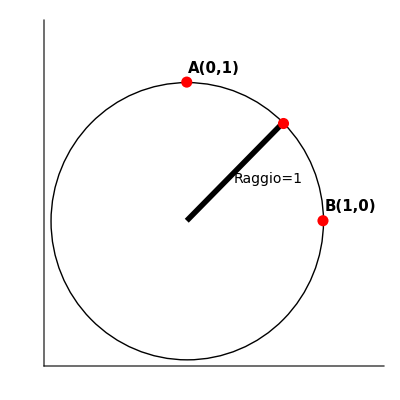

```mathematica
DisegnaCirconferenzaInit[]
```

## Seno e Coseno

Prendiamo la circonferenza goniometrica e un angolo orientato α, chiamiamo:
    - Coseno  di α, e indichiamo con cos(α), l’ascissa del punto P
    - Seno  di α, e indichiamo con sin(α), l'ordinata del punto P

```mathematica
DisegnaCirconferenza[]
```

Possiamo vedere come al variare dell’angolo varino seno e coseno, dunque siamo in grado di definire le funzioni tali per cui ad ogni angolo vengano associati i rispettivi seno e coseno. 
Il dominio di queste funzioni è ℝ, infatti possiamo prendere un qualsiasi angolo, immaginando eventualemente di poter fare più giri. Per quanto riguarda il codominio, occorre notare che la circonferenza ha raggio unitario, dunque le coordinate variano tra -1 e 1.

-Graphics-

Osserviamo che quando l'angolo α supera l'angolo giro, il punto P torna sui suoi passi, percorrendo nuovamente la circonferenza. Questo significa che le sue coordinate si ripetono, e cosi' il seno ed il coseno. Da cio' possiamo dedurre che ad ogni giro, ovvero ogni 2π radianti, le funzioni goniometriche assumono gli stessi valori. 
In linguaggio matematico  si dice che le funzioni seno e coseno sono funzioni periodiche di periodo 2π. Vale che

Inoltre osserviamo che

-Graphics- -Graphics-

## Prima relazione fondamentale

Abbiamo visto che l’equazione della circonferenza goniometrica è x^2+ y^2 = 1 dove x e y sono rispettivamente l’ascissa (coseno) e l’ordinata (seno) di un punto appartenente all circonferenza 
Dunque cos^2(α) + sin^2(α) = 1, ∀α ∈ ℝ

```mathematica
GraficoPrimaRelazione[]
```

## Tangente

Definiamo la terza funzione goniometrica : la tangente. 
Preso un angolo orientato α, la sua tangente è definita come il rapporto tra sin(α) e cos (α).

									tan(α) = (sin(α))/(cos(α))

Come nei casi precedenti, è possibile definire una funzione tangent ma in questo caso il codominio è tutto ℝ
      
OSSERVAZIONE: per definizione di seno e coseno, la tangente di un angolo α è il rapporto tra l’ordinata e l’ascissa del punto associato

```mathematica
GraficoTangente[]
```

## Angoli Associati

Supponiamo di conoscere il valore che le funzioni goniometriche assumono per un particolare angolo α, possiamo velocemente ricavare i valori assunti su alcuni particolari angoli, detti associati di α.
Anzichè memorizzare i valori del seno e del coseno di ogni angolo importante vediamo come è possibile ricavare tali valori di attaverso l’utilizzo dei seguenti quattro angoli:

0

```mathematica
AngoliAssociati0[]
```

π/4 ~ 45°

```mathematica
AngoliAssociati45[]
```

π/6 ~ 30°

```mathematica
AngoliAssociati30[]
```

π/3 ~ 60°

```mathematica
AngoliAssociati60[]
```

## Triangoli

Consideriamo un triangolo rettangolo qualsiasi. Vogliamo ricavare le sue proprietà utilizzando ciò che sappiamo della goniometria. 
Preso il triangolo ABC, retto in C, tracciamo la circonferenza goniometrica di centro A.

//immagine: con colori coerenti a seno e coseno

-Graphics-

I triangoli ABC e APH sono simili, perciò il rapporto tra i lati è costante, da cui ricaviamo che:
     									 
-Graphics-
      e poiché      -Graphics-     vale   -Graphics-
     
      
      Possiamo riformularle in questo modo:
      Cateto =  ipotenusa x seno dell'angolo (α) opposto 
      Cateto= ipotenusa(c) x coseno dell'angolo (β) acuto adiacente  			 -Graphics-
      cateto= altro cateto(b) * tangente dell'angolo (α) opposto al primocateto-Graphics-

Molto importante è quest’ultima formula perchè ci servirà per determinare l’altezza di una torre.

## Teorema del seno

In un triangolo le misure dei lati sono proporzionali ai seni degli angoli opposti:

-Graphics-                    -Graphics-

## Teorema del coseno

In un triangolo di lati a, b, c, vale la seguente formula:

-Graphics-		-Graphics-

Mettiti alla Prova 	  			 Ma a cosa serve tutto ciò? -Graphics-

# ESERCIZI

## Individua le Coordinate

Individua le coordinate x ed y del punto rosso situato nel piano cartesiano:

```mathematica
EsCoordinate[]
```

## Distanza tra due Punti

```mathematica
EsDistanze[]
```

## Seno e Coseno

```mathematica
EsSinCos[]
```

-Graphics- Ripasso	  			 Ma a cosa serve tutto ciò? -Graphics-

# APPLICAZIONI

Ora abbiamo gli strumenti per calcolare alcune misure tra cui l’altezza di una torre oppure la distanza che intercorre tra uno o due punti inaccessibili.

## Altezza di una torre

```mathematica
AltezzaTorre[]
```

```mathematica
Mettiti alla Prova -Graphics-	  		 -Graphics- Ripasso
```

alla Mettiti Prova -Graphics- Ripasso -Graphics-